# Projekt 1l - Matematisk statistik IX1501

Ninous Essac: ninous@kth.se
Angelina Mallo: mallo@kth.se

## The Relative Error of Normal Approximation

### Uppgift

If you consider the average of 20 iid rvs, normal distribution is often considered as a good approximation. However in this task you will go beyond this recommendation and study under what circumstances it is valid. The exponential distribution is very skew compared to the uniform distribution. How is this effecting the approximation with normal distribution?

In a certain cellular phone system new calls arrives with exponential distributed interarrivaltimes with expectation value μ=λ^-1=3 minutes. The interarrivaltime is the time between two incoming calls.

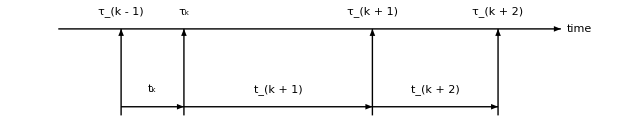

#### Task

Study the average t̄=1/n ∑_(k=1)^n t_k of n=20 interarrival times. Plot the absolute error of the pdf_(t̄)(t) and the cdf_(t̄)(t) using the normal approximation. Make also a plot of the relative error of

P(t̄>x), μ-2σ/√n<x<μ+2σ/√n

Conclusion? Is the approximation always useful?

Hint: The sum of iid exponential rvs has a well-known distribution, which is built-in in Mathematica, ErlangDistribution[n,λ] or GammaDistribution[n,1/λ].

Study the number of incoming calls during one hour. Plot the absolute and relative error of the probability function using normal approximation. Conclusion?

Hint: What is the distribution of the number of events in a certain time interval, e.g 1h, if the time between the events is exponential?

### Sammanfattning

#### Task I

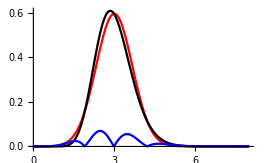
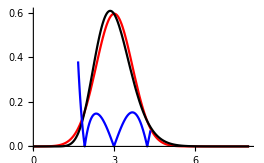
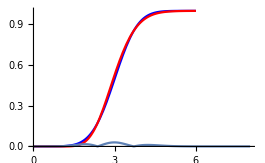
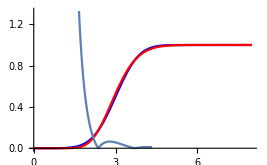
I den första deluppgiften (task I) skulle vi studera funktionen  t̄=1/n ∑_(k=1)^n t_k of n=20. Vi plottade absoluta error och relativa error för  pdf_(t̄)(t) och cdf_(t̄)(t) genom att använda normalapproximation för att komma till en slutsats om approximationen alltid är användbar. 

-Graphics-
fig.1 Absoluta error PDF.

-Graphics-
fig.2 Relativa error PDF.

-Graphics-
fig.3 Absoluta error för CDF.

-Graphics-
fig 4. Relativa error för CDF.

#### Task II

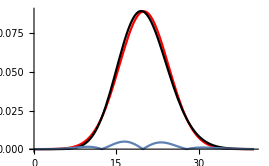
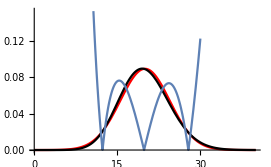
I den andra deluppgiften (task II) skulle vi studera antalet inkomna samtal och plotta både absoluta och relativa error för sannolikhetsfunktionen genom att använda normalapproximation. 

-Graphics-
fig.5 Absoluta error för PDF.

-Graphics-
fig.6 Relativa error för PDF.

### Diskussion

If you consider the average of 20 iid rvs, normal distribution is often considered as a good approximation. However in this task you will go beyond this recommendation and study under what circumstances it is valid. The exponential distribution is very skew compared to the uniform distribution. How is this effecting the approximation with normal distribution?

Den centrala gränsvärdesatsen säger att vi kan approximera med normalfördelningen istället för exponentialfördelningen så länge vi har tillräckligt stora n-värden.

#### Task 1

För att kunna bestämma felen mellan approximation och exakt värde bestäms de med olika fördelningar, approximation bestäms med hjälp av normalfördelningen medan det exakta värdet beräknas med gammafördelning eftersom fördelningen är kontinuerlig. 

Vi plottar sedan absoluta och relativa errorn för att se differensen mellan approximationen och det exakta värdet. Felet förändras beroende på längd. 

Absoluta felet beräknas som differensen mellan approximation och exakta värde medan relativa felet beräknas som differensen mellen approximation och exakta värde dividerat med det exakta värdet, vilket gör att vi får felet i procent. 

Conclusion? Is the approximation always useful?
Ju mindre n är desto mer utmärks skillnaden mellan det approximerade värdet och det exakta värdet. Skulle vi ha ett större intervall skulle resultatet bli mer exakt. Även för mindre n får vi en nära approximation av det exakta värdet.

#### Task II

I denna uppgift undersöker vi antal inkommande samtal under en timme, därför blir väntevärdet 20, vilket innebär att vi måste normalfördela värdet. 

Poissonfördelningen används eftersom vi undersöker en slumpmässig händelse i en tidsperiod där händelserna är oberoende av varandra. Precis som tidigare plottas nu de båda fördelningarna tillsammans med antingen absoluta eller relativa felet. 

Conclusion?
Med normalfördelningen fick vi en bra approximation i jämförelse med possionfördelningen som gav det exakta värdet.

### Kod - Task 1

```mathematica
n:=20
```

```mathematica
µ=3;
```

```mathematica
λ:=1/µ
```

```mathematica
σ=StandardDeviation[ExponentialDistribution[λ]];
```

```mathematica
normalFordelning:=NormalDistribution[µ,(σ/(√n))]
pdfNF:=PDF[normalFordelning,x]
```

```mathematica
gammaFordelning:=GammaDistribution[n,((1/λ)/n)]
pdfGF:=PDF[gammaFordelning,x]
```

```mathematica
PlotNF=Plot[pdfNF,{x,0,6},PlotRange-> All,PlotStyle-> {Red}];
PlotGF=Plot[pdfGF,{x,0,6},PlotRange-> All,PlotStyle-> {Black}];
```

```mathematica
absoluteError:=Abs[pdfGF-pdfNF]
PlotAE:=Plot[absoluteError,{x,0,6},PlotRange-> All,PlotStyle-> {Blue}];
```

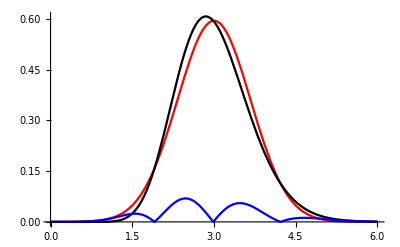

```mathematica
Show[PlotNF,PlotGF,PlotAE]
```

```mathematica
relativeError:=Abs[(pdfGF-pdfNF)/pdfGF];
PlotRE:=Plot[relativeError,{x,µ-(2 σ/(√n)),µ+(2 σ/(√n))},PlotRange-> All,PlotStyle-> {Blue}]
```

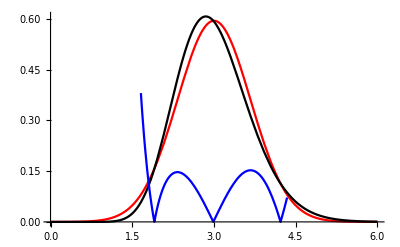

```mathematica
Show[PlotNF,PlotGF,PlotRE]
```

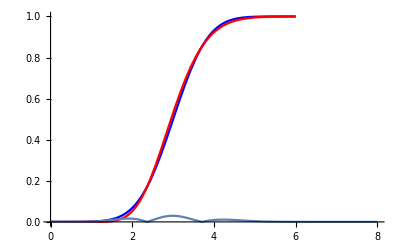

```mathematica
absoluteErrorCDF[x_]:=Abs[CDF[normalFordelning,x]-CDF[gammaFordelning,x]];
PlotAEcdf=Plot[absoluteErrorCDF[x],{x,0,8},PlotRange-> All];
Show[cdfNormalFordelning,cdfGammaFordelning,PlotAEcdf]
```

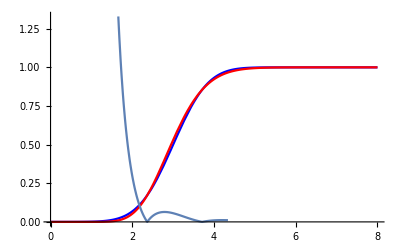

```mathematica
relativeErrorCDF[x_]:=Abs[((CDF[gammaFordelning,x])-(CDF[normalFordelning,x]))/CDF[gammaFordelning,x]];
PlotREcdf=Plot[relativeErrorCDF[x],{x,µ-((2σ)/(√n)),µ+((2σ)/(√n))},PlotRange-> All];
Show[cdfNormalFordelning,cdfGammaFordelning,PlotREcdf]
```

### Kod - Task 11

```mathematica
ClearAll["`*"] (*Clear everything*)
```

```mathematica
n:=20
```

```mathematica
µ:=20
```

```mathematica
λ:=1/µ
```

```mathematica
σ=StandardDeviation[ExponentialDistribution[λ]];
NF=NormalDistribution[µ,(σ/(√n))];
pdfNF:=PDF[NF,x]
PlotPdfNF:=Plot[pdfNF,{x,0,40},PlotRange-> All,PlotStyle-> {Red}]
```

```mathematica
PF = PoissonDistribution[µ];
pdfPF = PDF[PF,x];
PlotPdfPF = Plot[pdfPF,{x,0,40},PlotRange->All,PlotStyle-> {Black}];
```

```mathematica
absoluteError= Abs[pdfPF-pdfNF];
plotAbsoluteError = Plot[absoluteError,{x,0,40},PlotRange->All];
```

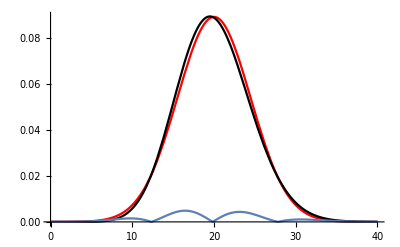

```mathematica
Show[PlotPdfNF,PlotPdfPF,plotAbsoluteError]
```

```mathematica
relativeError = Abs[(pdfPF-pdfNF)/pdfPF];
PlotRE=Plot[relativeError,{x,10,30}];
```

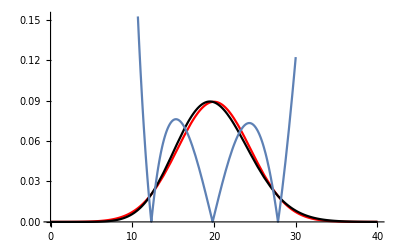

```mathematica
Show[PlotPdfNF,PlotPdfPF,PlotRE]
```